#### BC_Checkerboard.nb: Calculate and display a matrix (checkerboard) of angles among elastic maps. INSTRUCTIONS: Run common_funs, ChooseTmat, BC_CumulativeBeta. The elastic map is specified in BC_CumulativeBeta.nb The notebook takes about 30 seconds to run.

#### directories (see ChooseTmat.nb) For PrintFigures=True to work, you need create the directory pdf_print/ inside elasticity/

```mathematica
MatrixNote[Tmat]
```

```mathematica
PrintFigures=True;
```

```mathematica
mdir
odir=FileNameJoin[{mdir,"pdf_print"}]
```

```mathematica
WantNumbers="WantNumbers"; (* display text numbers within each colored matrix entry *)
```

```mathematica
numdigmat=1; (* number of digits to display in matrix entries *)
```

#### Functions

```mathematica
ListSigmaOfΣn[Σn_]:=Join[Σn/@domain[Σn],ListComplement[ListSigmaAll,Σn/@domain[Σn]]]
```

```mathematica
ListSigmaOfΣn[ΣnTETXISO]
ListSigmaOfΣn[ΣnTETCUBE]
ListSigmaOfΣn[ΣnTRIGCUBE]
ListSigmaOfΣn[ΣnTRIGXISO]
```

```mathematica
SigmaPairsMatrix[Σn_,dim_]:=Table[{Take[ListSigmaOfΣn[Σn],dim][[j]],Take[ListSigmaOfΣn[Σn],dim][[k]]},{j,dim},{k,dim}];
```

#### Example

```mathematica
MatrixForm[SigmaPairsMatrix[ΣnTETCUBE,6]]
```

#### Here is how the Map function works .

```mathematica
MatrixForm[Map[#[[1]]+#[[2]]&,SigmaPairsMatrix[ΣnTETCUBE,6],{2}]]
```

```mathematica
InternodalAngles[Tmat_,Σn_,nm_,dim_]:=Map[Chop[MakeReal[AngleMatrix[SmatOfΣ[#[[1]],Tmat,Σn,nm],SmatOfΣ[#[[2]],Tmat,Σn,nm]]/Degree],0.0001]&,SigmaPairsMatrix[Σn,dim],{2}];
```

#### Example Choose node mode and node sequence (precomputed in BC_CumulativeBeta.nb)

```mathematica
nm=nm2; Σn=ΣnTETXISO;
MatrixNote[Tmat]
TextNodeMode[nm]
ListSigmaOfΣn[Σn]
MatrixForm[InternodalAngles[Tmat,Σn,nm,6]]
MatrixForm[InternodalAngles[Tmat,Σn,nm,8]]
```

```mathematica
rrow[i_,Tmat_,Σn_,nm_,dim_]:=Join[{Take[ListSigmaOfΣn[Σn],dim][[i]]},InternodalAngles[Tmat,Σn,nm,dim][[i]]];
rrow[0,Tmat_,Σn_,nm_,dim_]:=Join[{""},Take[ListSigmaOfΣn[Σn],dim]];
```

#### Example

```mathematica
Σn=ΣnTETCUBE;dim=8;
rrow[0,Tmat,Σn,nm2,dim]
rrow[3,Tmat,Σn,nm2,dim]
```

```mathematica
dim=6;
MatrixNote[Tmat]
TextNodeMode[nm]
MatrixForm[Table[rrow[i,Tmat,Σn,nm,dim],{i,0,dim}]]
```

```mathematica
gg[i_,j_,Tmat_,Σn_,nm_,dim_]:=InternodalAngles[Tmat,Σn,nm,dim][[i,j]];
```

#### Example

```mathematica
MatrixNote[Tmat]
TextNodeMode[nm]
gg[4,5,Tmat,ΣnTETXISO,nm,6]
```

```mathematica
Sort[Flatten[InternodalAngles[Tmat,Σn,nm,8]]]
```

```mathematica
ForScaling:=Max[Flatten[InternodalAngles[Tmat,ΣnTETXISO,nm2,8]]]; (* May need to change *)
```

```mathematica
ForScaling
```

#### For legends. The setting increment = n prints every n^th contour label.

```mathematica
hw=1.5;fontsize=15;increment=2;offset=2.5;
Show[legends[Range[0,24,4],22,SubscriptBox[Style["α",20],Style["MONO",11]]//DisplayForm,hw,fontsize,increment,offset],ImageSize->100,PlotRange->All]
```

#### Original functions

```mathematica
(* ListSigmaOfΣn[Σn_]:=Join[Σn/@domain[Σn],ListComplement[ListSigmaAll,Σn/@domain[Σn]]]
SigmaPairsMatrix[Σn_,dim_]:=Table[{Take[ListSigmaOfΣn[Σn],dim][[j]],Take[ListSigmaOfΣn[Σn],dim][[k]]},{j,dim},{k,dim}];
InternodalAngles[Tmat_,Σn_,nm_,dim_]:=Map[Round[AngleMatrix[SmatOfΣ[#[[1]],Tmat,Σn,nm],SmatOfΣ[#[[2]],Tmat,Σn,nm]]/Degree,.01]&,SigmaPairsMatrix[Σn,dim],{2}];
gg[i_,j_,Tmat_,Σn_,nm_,dim_]:=InternodalAngles[Tmat,Σn,nm,dim][[i,j]];
PreCheckerboard[Tmat_,Σn_,nm_,dim_,ForScaling_,WantNumbers_]:={Table[{FaceForm[ColorData["TemperatureMap"][gg[i,j,Tmat,Σn,nm,dim]/ForScaling]],Cuboid[{i-.5,-j-.5},{i+.5,-j+.5}]},{i,dim},{j,dim}],
If[WantNumbers=="WantNumbers",Table[Text[Style[Round[gg[i,j,Tmat,Σn,nm,dim],.1],13],{i,-j}],{i,dim},{j,dim}]]}; *)
```

#### New Functions

```mathematica
PreCheckerboard[Tmat_,Σn_,nm_,dim_,ForScaling_,showNumbers_,showDiagonalSums_]:=
PreCheckerboard[Tmat,Σn,nm,dim,ForScaling,showNumbers,showDiagonalSums]=Module[{matrix,diagonalSums,additionalElements,numStyle},matrix=Table[gg[i,j,Tmat,Σn,nm,dim],{i,dim},{j,dim}];
diagonalSums=If[TrueQ[showDiagonalSums],Prepend[Table[Sum[matrix[[i,Min[dim-k+i,dim]]],{i,1,Min[k,dim]}],{k,1,dim-1}],""],{}];
numStyle=Style[NumberForm[#,{Infinity,numdigmat}],13]&;
additionalElements={Table[{FaceForm[ColorData["TemperatureMap"][matrix[[i,j]]/ForScaling]],Cuboid[{i-.5,-j-.5},{i+.5,-j+.5}]},{i,dim},{j,dim}],If[TrueQ[showNumbers],Flatten@{Table[Text[numStyle[matrix[[i,j]]],{i,-j}],{i,dim},{j,dim}],If[TrueQ[showDiagonalSums],Table[Text[numStyle[diagonalSums[[i]]],{dim+1,-i}],{i,2,Length[diagonalSums]}],{}]},{}]};
Flatten[additionalElements]]
```

```mathematica
sizeA=350;
sizeB=475;
labelFontSize=13; 
dxleft=0.3;
dytop=-0.1; 
Checkerboard[Tmat_,Σn_,nm_,dim_,ForScaling_,showNumbers_,showDiagonalSums_,showLegends_]:=Module[{legendInset,graphicsElements},(*Define the legend inset if required*)legendInset=If[TrueQ[showLegends],Inset[legends[Range[0,5+ForScaling,5],ForScaling,"",hw,fontsize,increment,offset],{3+dim,-3},Center,1.8],Nothing];
graphicsElements={Style[Text[#,{dxleft,-Position[Take[ListSigmaOfΣn[Σn],dim],#][[1,1]]},{Right,Center}],labelFontSize]&/@Take[ListSigmaOfΣn[Σn],dim],Style[Text[#,{Position[Take[ListSigmaOfΣn[Σn],dim],#][[1,1]],dytop},{Center,Center}],labelFontSize]&/@Take[ListSigmaOfΣn[Σn],dim],PreCheckerboard[Tmat,Σn,nm,dim,ForScaling,showNumbers,showDiagonalSums]};
Labeled[Graphics[Flatten[{graphicsElements,legendInset}],ImageSize->If[TrueQ[showLegends],sizeB,sizeA]],Style[SequenceForm[MatrixNote[Tmat],"  [",nm,"]"],14,FontFamily->"Arial"],{{Bottom,Left}}]]
```

## Examples

```mathematica
Checkerboard[Tmat,ΣnTETXISO,nm2,6,ForScaling,True,True,True]
```

```mathematica
Checkerboard[Tmat,ΣnTETXISO,nm2,6,ForScaling,True,True,False]
```

```mathematica
Checkerboard[Tmat,ΣnTETXISO,nm2,6,ForScaling,True,False,False]
```

```mathematica
Checkerboard[Tmat,ΣnTETXISO,nm2,6,ForScaling,False,False,False]
```

#### you can plot all 8 Σ, but only for nm1 and nm2 with the columns added past ISO, the cumulative angles are less relevant

```mathematica
Checkerboard[Tmat,ΣnTETXISO,nm2,8,ForScaling,True,True,False]
```

## Merge plots into one

```mathematica
Σn=ΣnTETXISO;
dim=nMax[Σn];
MatrixNote[Tmat]
Print[" UforNM1 = ", DispMat[UforNM1,2]];
```

```mathematica
(* Grid[{{Checkerboard[Tmat,Σn,nm1,dim,ForScaling,"WantNumbers","NoWantLegends"],
Checkerboard[Tmat,Σn,nm2,dim,ForScaling,"WantNumbers","noWantLegends"],
Checkerboard[Tmat,Σn,nm3,dim,ForScaling,"WantNumbers","WantLegends"]}}] *)
```

```mathematica
otag=FileNameJoin[{odir,"Checkerboard_"<>Tlab[Tmat]<>"_"}]
```

```mathematica
MakeFig[Σn_,PrintFigures_,showDiagonalSums_,showLegends_]:=Module[{suffix,ofile,fig},suffix=If[TrueQ[showLegends],"_legend",""];
fig=Grid[{{
Checkerboard[Tmat,Σn,nm1,nMax[Σn],ForScaling,True,showDiagonalSums,False],
Checkerboard[Tmat,Σn,nm2,nMax[Σn],ForScaling,True,showDiagonalSums,False],
Checkerboard[Tmat,Σn,nm3,nMax[Σn],ForScaling,True,showDiagonalSums,showLegends]}},Spacings->{{0,4,4},0}];
ofile=FileNameJoin[{otag<>StringDrop[ToString[Σn],2]<>suffix<>".pdf"}];
If[PrintFigures,Export[ofile,fig],fig]];
```

```mathematica
MakeFig[ΣnTETXISO,False,True,True]
MakeFig[ΣnTETXISO,False,False,True]
MakeFig[ΣnTETXISO,False,False,False]
```

```mathematica
MatrixNote[Tmat]
Print[" UforNM1 = ", DispMat[UforNM1,2]];
MakeFig[ΣnTETXISO,PrintFigures,False,True]
MakeFig[ΣnTETCUBE,PrintFigures,False,True]
MakeFig[ΣnTRIGCUBE,PrintFigures,False,True]
MakeFig[ΣnTRIGXISO,PrintFigures,False,True]
MakeFig[ΣnTETXISO,PrintFigures,False,False]
MakeFig[ΣnTETCUBE,PrintFigures,False,False]
MakeFig[ΣnTRIGCUBE,PrintFigures,False,False]
MakeFig[ΣnTRIGXISO,PrintFigures,False,False]
```

```mathematica
px=Checkerboard[Tmat,ΣnTETXISO,nm2,6,ForScaling,True,False,False];
```

```mathematica
If[PrintFigures,Export[otag<>StringDrop[ToString[Σn],2]<>"_single.pdf",px],px];
```

## For Reference (Brown for ΣnTETXISO only)

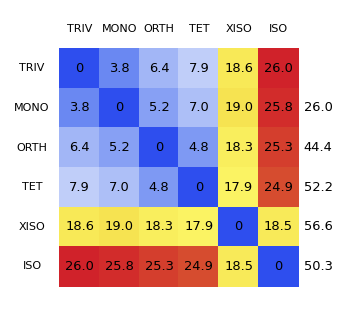
-Graphics-T is BrownAn00  [nm2]

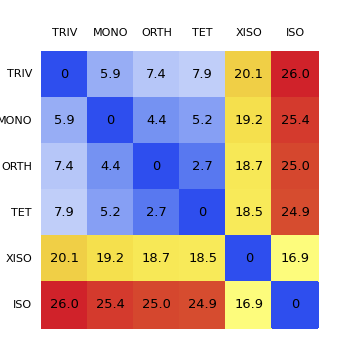
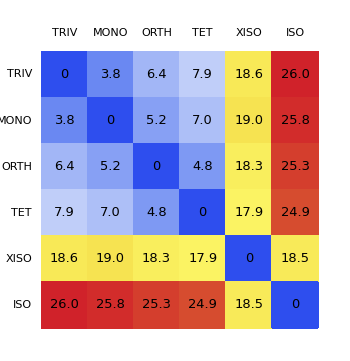
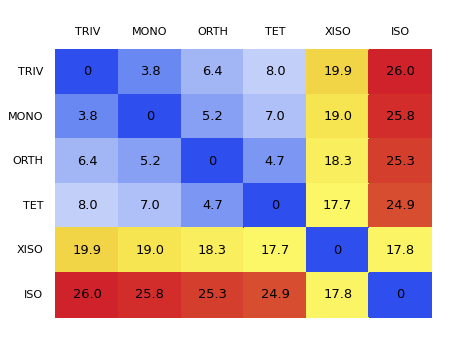
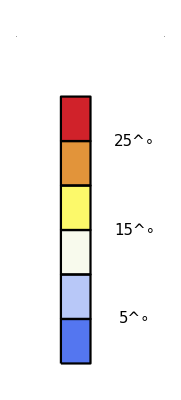
-Graphics-T is BrownAn00  [nm1] | -Graphics-T is BrownAn00  [nm2] | -Graphics-
-Graphics-T is BrownAn00  [nm3]